## Task 3. Finding the control matrix.

3.1. Finding the controllability matrix:

```mathematica
A={{1,-2},{2,-4}};
B={{-1},{4}};
t1=4;
U[t_]=MatrixExp[-A t].B;
ControlMatrix[T_]=Integrate[U[t].Transpose[U[t]],{t,0,T}];
```

3.2. Now, getting the concrete value of N:

```mathematica
N[ControlMatrix[t1]]
```

{{3.97324×10^10,7.94657×10^10},{7.94657×10^10,1.58933×10^11}}

3.3.1*. Checking our predicted value using estimate with delta (see original homework file):

```mathematica
d[T_]=Integrate[(1-Exp[3t])^2/9,{t,0,T}];
PredictedControlMatrix[T_]=d[T]*A.B.Transpose[B].Transpose[A];
N[PredictedControlMatrix[t1]]
```

{{3.97327×10^10,7.94654×10^10},{7.94654×10^10,1.58931×10^11}}

3.3.2*. Debugging the relative difference between the actual and predicted values:

```mathematica
e=N[Norm[ControlMatrix[t1]-PredictedControlMatrix[t1]]/Norm[ControlMatrix[t1]]]
```

0.0000132869

3.4. Checking inverse existence and whether N is positive-definite
3.4.1. Inverse:

```mathematica
InverseControlMatrix[T_]=Inverse[ControlMatrix[T]];
N[InverseControlMatrix[t1]]
```

{{0.033333,-0.0166663},{-0.0166663,0.00833304}}

3.4.2. Positive-definiteness:

```mathematica
D1=N[ControlMatrix[t1][[1]][[1]]];
D2=N[Det[ControlMatrix[t1]]];
positiveDefinite=(D1>0)&&(D2>0)
```

True

## Task 4. Control

4.1. Finding control function u(t):

```mathematica
Clear[x0,u]
x0={{-2},{0}};
u[t_]=-Transpose[U[t]].InverseControlMatrix[t1].x0;
u[t_]=Simplify[u[t][[1]][[1]]];
N[u[t]]
```

2.51675×10^-12 (-7.9467×10^10-30. 2.71828^(3. t)+6. 2.71828^(3. (4.+t)))

4.2. Finding explicit expressions for trajectory (x_1(t), x_2(t)):

```mathematica
Clear[x1,x2,t]
solution=DSolve[{x1'[t]==x1[t]-2x2[t]-u[t],x2'[t]==2x1[t]-4x2[t]+4u[t],x1[0]==-2,x2[0]==0},{x1[t],x2[t]},t];
x1[t_]=solution[[1]][[1]][[2]];
x2[t_]=solution[[1]][[2]][[2]];
```

4.3. Plotting the trajectory below:

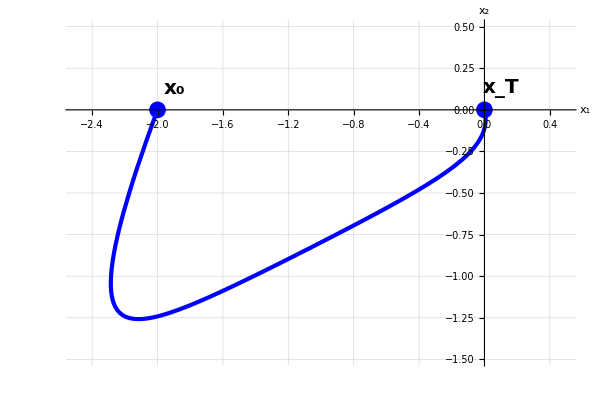

```mathematica
trajectory[t_]=Evaluate[{x1[t],x2[t]}/.solution];
Show[
ParametricPlot[trajectory[t],{t,0,4},PlotStyle->Directive[Blue,Thickness[0.005]]]/.Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.}],Arrow[x]},
ListPlot[{Labeled[{-2,0},"x_0"],Labeled[{0,0},"x_T"]},PlotStyle->Directive[Blue,PointSize[0.02]],LabelStyle->{20,Bold}],
GridLines->Automatic,
ImageSize->600,
AxesLabel->{"x_1","x_2"},
LabelStyle->{14,FontFamily},
AxesStyle->Arrowheads[{0.0,0.05}],
PlotRange->{{-2.5,0.5},{-1.5,0.5}}
]
```